```mathematica
knownMass = 39.962590863; 
mUnknown = 36;
knownSecFreqs = 2*π*MHz*{.71, 1.3242, 1.6096}; (*Frequencies from Hao's Calibration on 06-04 - keep these and if need to change override later*)
knownSecFreqs = 2*π*MHz*{.7108, 1.3, 1.6}; 
massArr = {knownMass, mUnknown, knownMass};
EField ={0,0,0};
numIons = Length[massArr];
ionPositions = Table[{x[i], y[i], z[i]}, {i, numIons}];
ΩRF = 2*π*19.0696 * MHz;
```

```mathematica
qe = 1.60217663*10^-19;
e0 = 8.8541878188*10^-12;
kHz = 10^3;
MHz = 10^6;
nm = 10^-9;
μm = 10^-6;
mm = 10^-3;
amu = 1.66053904*10^-27;
r0 = 550 * μm;
κ = 0.077;
h = 6.62607015*10^-34;
ℏ = h/(2*π);
```

```mathematica
(*Calculate mass independent mathieu equations*)
getMathieuParams[knownSecFreqs_, knownMass_, ΩRF_]:= Module[{knownSecFreqsSorted, ar, az, qx},
knownSecFreqsSorted = knownSecFreqs[[Ordering[knownSecFreqs]]];
ar = 2/ΩRF^2*(knownSecFreqsSorted[[3]]^2-knownSecFreqsSorted[[2]]^2);
az = 4/ΩRF^2*knownSecFreqsSorted[[1]]^2;
qx = Sqrt[8*knownSecFreqsSorted[[3]]^2/ΩRF^2-(ar-2*az)];
{ar, az, qx}*knownMass
]
```

```mathematica
getMassIndepSecFreqs[massIndepMathieuParams_, massArr_, ΩRF_]:= Module[{arMassIndep, azMassIndep, qxMassIndep,
independentAxialFreqs, independentEGGsFreqs, independentRFFreqs},
arMassIndep = massIndepMathieuParams[[1]];
azMassIndep = massIndepMathieuParams[[2]];
qxMassIndep = massIndepMathieuParams[[3]];
independentAxialFreqs = Sqrt[azMassIndep/massArr*ΩRF^2/4];
independentEGGsFreqs = Sqrt[((qxMassIndep/massArr)^2+(arMassIndep/massArr-2*azMassIndep/massArr))*ΩRF^2/8];
independentRFFreqs= Sqrt[independentEGGsFreqs^2-ΩRF^2/2*arMassIndep/massArr];
{independentAxialFreqs, independentRFFreqs, independentEGGsFreqs}]
```

```mathematica
getPotential[massArr_, massIndepSecFreqs_, numIons_, EField_, ionPositions_,
β_:0]:=Module[{independentAxialFreqs, independentEGGsFreqs,independentRFFreqs,
Utrap, UColoumb, UField, Uanharmonic, U, EFieldMat},
EFieldMat =ConstantArray[EField, numIons];
independentAxialFreqs = massIndepSecFreqs[[1]];
independentRFFreqs = massIndepSecFreqs[[2]];
independentEGGsFreqs = massIndepSecFreqs[[3]];
Utrap = Sum[massArr[[i]]/2*amu*(independentRFFreqs[[i]]^2*x[i]^2+independentEGGsFreqs[[i]]^2*y[i]^2+independentAxialFreqs[[i]]^2*z[i]^2), {i, 1, numIons}];
UColoumb = qe^2/(4*π*e0)*Sum[Sum[ 1/Sqrt[(x[i]-x[j])^2+(y[i]-y[j])^2+(z[i]-z[j])^2], {i,1, j-1}], {j, 1, numIons}];
UField = -qe*Total[Flatten[ionPositions*EFieldMat]];
Uanharmonic = Sum[β*z[i]^3, {i, 1, numIons}];
U = Utrap+UColoumb+UField+Uanharmonic;
U
]
```

```mathematica
getEquilibriumPositions[U_,numIons_, ionEqPositions_] :=Module[{zGuess, guessPositions, ionEquilibriumPositions}, 
zGuess = 10*Flatten[Table[{i}, {i, -(numIons-1)/2, (numIons-1)/2,1}]]*μm;
guessPositions = Flatten[Table[{{z[i],zGuess[[i]]}, {y[i],0}, {x[i],0}}, {i,1,numIons}],1];
ionEquilibriumPositions = FindRoot[Table[D[U, q]==0, {q, Flatten[ionPositions]}],guessPositions];
ionEquilibriumPositions]
```

```mathematica
getModeParams[U_, massArr_, ionEquilibriumPositions_, numIons_,ionPositions_]:= Module[{evals, evecs,
M, H, orderingIndices, evecsSorted, evecsNormalized, evalsSorted, secFreqsMHz},
H = D[U, {Flatten[ionPositions], 2}]/.ionEquilibriumPositions;
M = DiagonalMatrix[Flatten[Table[massArr[[i]]*amu*{1,1,1}, {i, numIons}]]];
{evals, evecs} = Eigensystem[Sqrt[Inverse[M]].H.Sqrt[Inverse[M]]];
orderingIndices = Ordering[evals];
evecsSorted = evecs[[orderingIndices]];
evecsNormalized = Chop[Table[Normalize[evecsSorted[[idx]]], {idx, Length[evecsSorted]}]];
evalsSorted = evals[[orderingIndices]];
secFreqsMHz = Chop[Sqrt[evalsSorted]/(2*π*MHz)];
{evecsNormalized, secFreqsMHz}
]
```

```mathematica
overlapScore[axialRock_, vec_] := Abs[Conjugate[axialRock].vec]^2
getAxialRock[{vecs_, vals_}]:= Module[{axialRockBasis, scores, idx},
axialRockBasis = {0,0,-1,0,0,1,0,0,-1};
scores = overlapScore[axialRockBasis, #] & /@ vecs;
idx = First @ Ordering[scores, -1];
vals[[idx]]
]
```

```mathematica
SimDiffSecFreqs[Sec1_, Sec2_, Sec3_, voltRange_:20]:=Module[{singleIonSecFreqs, SecFreqs, maxSecFreqShift},
singleIonSecFreqs = 2*π*MHz*{Sec1, Sec2, Sec3};
simVoltageList = Table[Voltage,  {Voltage, -voltRange/2+voltMidPoint, voltRange/2+voltMidPoint,0.25}];
secFreqs = Table[getAxialRock[getSecFreqs[{(κ*(Volt-voltMidPoint))/Sqrt[2],(κ*(Volt-voltMidPoint))/Sqrt[2],0}, massArr, singleIonSecFreqs, knownMass, numIons, ionPositions]], {Volt, simVoltageList}];
maxSecFreqShift = (Max[secFreqs] - Min[secFreqs]);
maxSecFreqShift*MHz
]
```

```mathematica
getSecFreqs[EField_, 
massArr_, knownSecFreqs_, knownMass_, numIons_, ionPositions_, β_:0]:= Module[{massIndepMathieuParams, massIndepSecFreqs, U, evecsNormalized, secFreqsMHz, ionEqPositions},
massIndepMathieuParams= getMathieuParams[knownSecFreqs, knownMass, ΩRF];
massIndepSecFreqs = getMassIndepSecFreqs[massIndepMathieuParams, massArr, ΩRF];
U = getPotential[massArr, massIndepSecFreqs, numIons, EField, ionPositions, β];
ionEqPositions = getEquilibriumPositions[U, numIons, ionPositions] (*this must be a different name*);
{evecsNormalized, secFreqsMHz} = getModeParams[U, massArr, ionEqPositions, numIons,ionPositions];
{evecsNormalized, secFreqsMHz}
]
```

```mathematica
{evecsNormalized, secFreqsMHz} = getSecFreqs[EField, massArr, knownSecFreqs, knownMass, numIons, ionPositions];

Table[Print[secFreqsMHz[[i]], ": ", evecsNormalized[[i]]], {i, 1, Length[secFreqsMHz]}];
```

0.722672: {0,0,0.59097,0,0,0.549098,0,0,0.59097}

0.838822: {0.508395,0,0,-0.695031,0,0,0.508395,0,0}

1.08847: {0.707107,0,0,0,0,0,-0.707107,0,0}

1.23114: {0,0,0.707107,0,0,0,0,0,-0.707107}

1.272: {0,-0.527415,0,0,0.666084,0,0,-0.527415,0}

1.3816: {0.491461,0,0,0.718979,0,0,0.491461,0,0}

1.43344: {0,0.707107,0,0,0,0,0,-0.707107,0}

1.68232: {0,0.470992,0,0,0.745877,0,0,0.470992,0}

1.77396: {0,0,-0.388271,0,0,0.835758,0,0,-0.388271}

## Axial Rocking Mode Shift

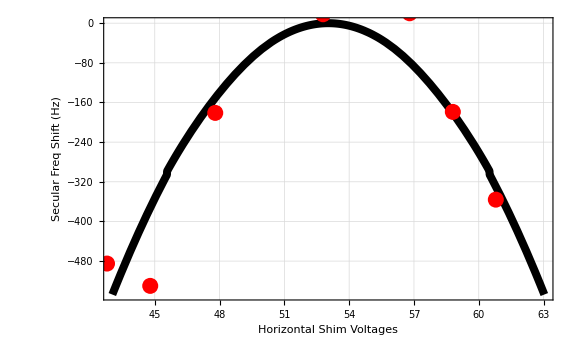

```mathematica
(*acutal data*)
actualVoltageList = {42.79, 62.79, 52.79, 44.79, 60.79, 47.8, 52.79, 57.8,55.79,52.79, 58.8, 56.8};
offsetSecFreqHz = {-485, -635, 18, -530, -356, -181, 72, 31, 82, 28, -179, 20};
actualData = Transpose@{actualVoltageList, offsetSecFreqHz};
voltRange = Max[actualVoltageList]-Min[actualVoltageList];
voltMidPoint = Mean[actualVoltageList];
nlm = NonlinearModelFit[actualData, -a*(x-b)^2+c,{a,b,c}, x, MaxIterations->1000];
voltMidPoint = ({a,b,c}/. nlm["BestFitParameters"])[[2]];

κ = 1.8;
simVoltageList = Table[Voltage,  {Voltage, -voltRange/2+voltMidPoint, voltRange/2+voltMidPoint,0.1}];
secFreqs = Table[getAxialRock[getSecFreqs[{(κ*(Volt-voltMidPoint))/Sqrt[2],(κ*(Volt-voltMidPoint))/Sqrt[2],0}, massArr, knownSecFreqs, knownMass, numIons, ionPositions]], {Volt, simVoltageList}];
maxSecFreq = Max[secFreqs];


Show[{Plot[(getAxialRock[getSecFreqs[{(κ*(Voltage-voltMidPoint))/Sqrt[2],(κ*(Voltage-voltMidPoint))/Sqrt[2],0}, massArr, knownSecFreqs, knownMass, numIons, ionPositions]]-maxSecFreq)*MHz,
{Voltage, -voltRange/2+voltMidPoint,voltRange/2+voltMidPoint}, PlotStyle->{Black, Thickness->0.01}],
ListPlot[Transpose@{actualVoltageList, offsetSecFreqHz}, PlotStyle->{Red, PointSize[0.02]}]},
FrameLabel->{Style["Horizontal Shim Voltages", 16], Style["Secular Freq Shift (Hz)", 16]}, ImageSize->Large, Frame->{{True, False}, {True, False}},
GridLines->Automatic
]
```

NonlinearModelFit::ivar: 2.99792×10^8 is not a valid variable.

Plot::plln: Limiting value -10.+NonlinearModelFit[{{42.79,-485},{62.79,-635},{52.79,18},{44.79,-530},{60.79,-356},{47.8,-181},{52.79,72},{57.8,31},{55.79,82},{52.79,28},«2»},2.99792×10^8-a (-b+x)^2,{a,b,2.99792×10^8},x,MaxIterations→1000][BestFitParameters] in {Voltage,-10.+«1»,10.+NonlinearModelFit[{{42.79,-485},{62.79,-635},{52.79,18},{44.79,-530},{60.79,-356},{47.8,-181},{52.79,72},{57.8,31},{55.79,82},{52.79,28},«2»},2.99792×10^8-a (Times[«2»]+x)^2,{a,b,2.99792×10^8},x,MaxIterations→1000][BestFitParameters]} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[{Plot[getSecFreqs[{Times[«3»],Times[«3»],0},massArr,knownSecFreqs,knownMass,numIons,ionPositions]⟦2⟧⟦9⟧,{Voltage,-voltRange/2+voltMidPoint,voltRange/2+voltMidPoint},PlotStyle→{Black,Thickness→0.01}],},FrameLabel→{Horizontal Shim Voltages,Secular Freq (2π MHz)},ImageSize→Large,Frame→{{True,False},{True,False}},PlotRange→All,GridLines→Automatic].

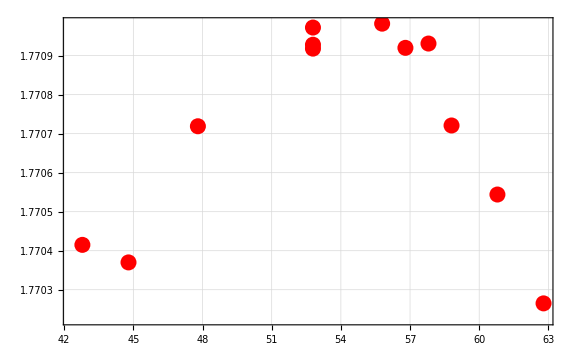
Show[{Plot[getSecFreqs[{(κ (Voltage-voltMidPoint))/(√2),(κ (Voltage-voltMidPoint))/(√2),0},massArr,knownSecFreqs,knownMass,numIons,ionPositions]⟦2⟧⟦9⟧,{Voltage,-voltRange/2+voltMidPoint,voltRange/2+voltMidPoint},PlotStyle→{Black,Thickness→0.01}],-Graphics-},FrameLabel→{Horizontal Shim Voltages,Secular Freq (2π MHz)},ImageSize→Large,Frame→{{True,False},{True,False}},PlotRange→All,GridLines→Automatic]

```mathematica
Show[{Plot[(getSecFreqs[{(κ*(Voltage-voltMidPoint))/Sqrt[2],(κ*(Voltage-voltMidPoint))/Sqrt[2],0}, massArr, knownSecFreqs, knownMass, numIons, ionPositions][[2]][[9]]),
{Voltage, -voltRange/2+voltMidPoint,voltRange/2+voltMidPoint}, PlotStyle->{Black, Thickness->0.01}],
ListPlot[Transpose@{actualVoltageList, offsetSecFreqHz/MHz+1.7709}, PlotStyle->{Red, PointSize[0.02]} ]},
FrameLabel->{Style["Horizontal Shim Voltages", 16], Style["Secular Freq (2π MHz)", 16]}, ImageSize->Large, Frame->{{True, False}, {True, False}}, PlotRange->All,GridLines->Automatic
]
```

### Axial COM Mode Shift

```mathematica
simVoltageList = Table[Voltage,  {Voltage, -voltRange/2+voltMidPoint, voltRange/2+voltMidPoint,0.1}];
secFreqs = Table[getSecFreqs[{(κ*(Volt-voltMidPoint))/Sqrt[2],(κ*(Volt-voltMidPoint))/Sqrt[2],0}, massArr, knownSecFreqs, knownMass, numIons, ionPositions][[2]][[1]], {Volt, simVoltageList}];
maxSecFreq = Max[secFreqs];

Show[{Plot[(getSecFreqs[{(κ*(Voltage-voltMidPoint))/Sqrt[2],(κ*(Voltage-voltMidPoint))/Sqrt[2],0}, massArr, knownSecFreqs, knownMass, numIons, ionPositions][[2]][[1]]- maxSecFreq)*MHz,
{Voltage, -voltRange/2+voltMidPoint,voltRange/2+voltMidPoint}, PlotStyle->{Black, Thickness->0.01}]},
FrameLabel->{Style["Horizontal Shim Voltages", 16], Style["Secular Freq Shift (2π Hz)", 16]}, ImageSize->Large, Frame->{{True, False}, {True, False}},
GridLines->Automatic
]
```

NonlinearModelFit::ivar: 2.99792×10^8 is not a valid variable.

General::stop: Further output of NonlinearModelFit::ivar will be suppressed during this calculation.

NonlinearModelFit::ivar: 2.99792×10^8 is not a valid variable.

Plot::plln: Limiting value -10.+NonlinearModelFit[{{42.79,-485},{62.79,-635},{52.79,18},{44.79,-530},{60.79,-356},{47.8,-181},{52.79,72},{57.8,31},{55.79,82},{52.79,28},«2»},2.99792×10^8-a (-b+x)^2,{a,b,2.99792×10^8},x,MaxIterations→1000][BestFitParameters] in {Voltage,-10.+NonlinearModelFit[{{42.79,-485},{62.79,-635},{52.79,18},{44.79,-530},{60.79,-356},{47.8,-181},{52.79,72},{57.8,31},{55.79,82},{52.79,28},«2»},«3»,MaxIterations→1000][BestFitParameters],10.+NonlinearModelFit[{{42.79,-485},{62.79,-635},{52.79,18},{44.79,-530},{60.79,-356},{47.8,-181},{52.79,72},{57.8,31},{55.79,82},{52.79,28},«2»},2.99792×10^8-a (Times[«2»]+x)^2,{a,b,2.99792×10^8},x,MaxIterations→1000][BestFitParameters]} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[{Plot[(getSecFreqs[«6»]⟦2⟧⟦1⟧-maxSecFreq) MHz,{Voltage,-voltRange/2+voltMidPoint,voltRange/2+voltMidPoint},PlotStyle→{Black,Thickness→0.01}]},FrameLabel→{Horizontal Shim Voltages,Secular Freq Shift (2π Hz)},ImageSize→Large,Frame→{{True,False},{True,False}},GridLines→Automatic].

Show[{Plot[(getSecFreqs[{(κ (Voltage-voltMidPoint))/(√2),(κ (Voltage-voltMidPoint))/(√2),0},massArr,knownSecFreqs,knownMass,numIons,ionPositions]⟦2⟧⟦1⟧-maxSecFreq) MHz,{Voltage,-voltRange/2+voltMidPoint,voltRange/2+voltMidPoint},PlotStyle→{Black,Thickness→0.01}]},FrameLabel→{Horizontal Shim Voltages,Secular Freq Shift (2π Hz)},ImageSize→Large,Frame→{{True,False},{True,False}},GridLines→Automatic]

## Axial Rocking Mode Shift Dependence on Single Ion Secular Frequencies

### Scan Wide Range of Secular Frequencies

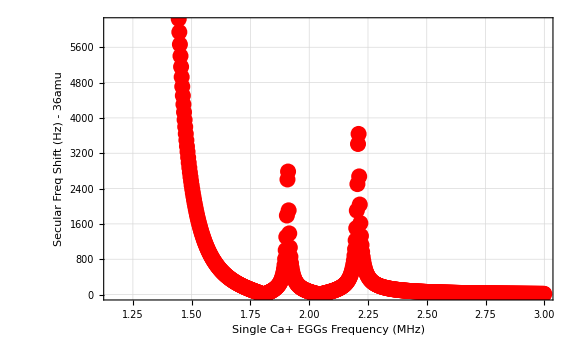

```mathematica
knownMass = 39.962590863; 
mUnknown = 36;
massArr = {knownMass, mUnknown, knownMass};
eggFreqSpan = Table[eggsFreq, {eggsFreq, 1.200, 3.000,.0025}];
freqShift = Table[SimDiffSecFreqs[.710,eggsFreq-.3,eggsFreq], {eggsFreq, eggFreqSpan}];
shiftData = Transpose@{eggFreqSpan, freqShift};
mass36Plot = ListPlot[shiftData, PlotStyle->{Red, PointSize[0.02]},
FrameLabel->{Style["Single Ca+ EGGs Frequency (MHz)", 16], Style["Secular Freq Shift (Hz) - 36amu", 16]}, ImageSize->Large, Frame->{{True, False}, {True, False}},
GridLines->Automatic]
```

```mathematica
Export["\\\\eric.physics.ucla.edu\\groups\\motion\\Mathematica\\cat_interferometer\\images\\axial_zz_stray_field_shift36.jpg", mass36Plot]
```

\\eric.physics.ucla.edu\groups\motion\Mathematica\cat_interferometer\images\axial_zz_stray_field_shift36.jpg

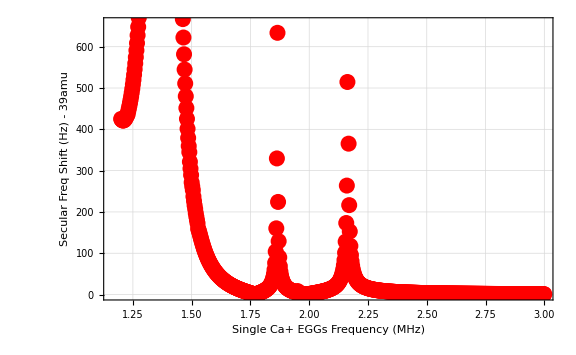

```mathematica
knownMass = 39.962590863; 
mUnknown = 39;
massArr = {knownMass, mUnknown, knownMass};
eggFreqSpan = Table[eggsFreq, {eggsFreq, 1.200, 3.000,.0025}];
freqShift = Table[SimDiffSecFreqs[.710,eggsFreq-.3,eggsFreq], {eggsFreq, eggFreqSpan}];
shiftData = Transpose@{eggFreqSpan, freqShift};
mass39Plot = ListPlot[shiftData, PlotStyle->{Red, PointSize[0.02]},
FrameLabel->{Style["Single Ca+ EGGs Frequency (MHz)", 16], Style["Secular Freq Shift (Hz) - 39amu", 16]}, ImageSize->Large, Frame->{{True, False}, {True, False}},
GridLines->Automatic]
```

```mathematica
SimDiffSecFreqs[.710,1.51-.3,1.51]
```

226.293

```mathematica
Export["\\\\eric.physics.ucla.edu\\groups\\motion\\Mathematica\\cat_interferometer\\images\\axial_zz_stray_field_shift39.jpg", mass39Plot]
```

\\eric.physics.ucla.edu\groups\motion\Mathematica\cat_interferometer\images\axial_zz_stray_field_shift39.jpg

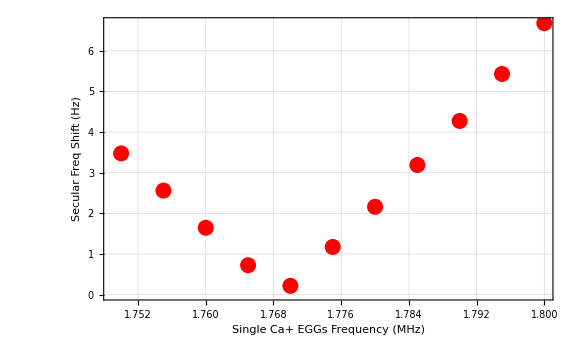

```mathematica
eggFreqSpan = Table[eggsFreq, {eggsFreq, 1.750, 1.800,.005}];
freqShift = Table[SimDiffSecFreqs[.710,eggsFreq-.3,eggsFreq], {eggsFreq, eggFreqSpan}];
shiftData = Transpose@{eggFreqSpan, freqShift};
ListPlot[shiftData, PlotStyle->{Red, PointSize[0.02]},
FrameLabel->{Style["Single Ca+ EGGs Frequency (MHz)", 16], Style["Secular Freq Shift (Hz)", 16]}, ImageSize->Large, Frame->{{True, False}, {True, False}},
GridLines->Automatic]
```

### Scan Narrowly about “nulls” where shift vanishes

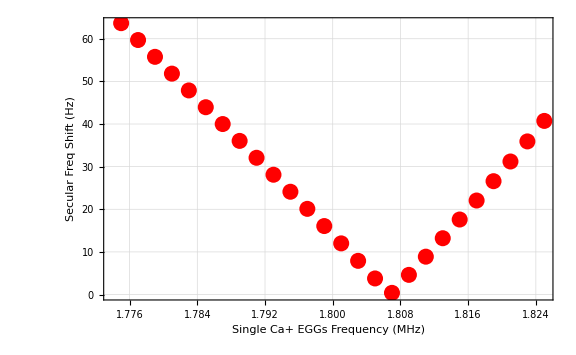

```mathematica
eggFreqSpan = Table[eggsFreq, {eggsFreq, 1.775, 1.825,.002}];
freqShift = Table[SimDiffSecFreqs[.710,eggsFreq-.3,eggsFreq], {eggsFreq, eggFreqSpan}];
shiftData = Transpose@{eggFreqSpan, freqShift};
firstNullPlot = ListPlot[shiftData, PlotStyle->{Red, PointSize[0.02]},
FrameLabel->{Style["Single Ca+ EGGs Frequency (MHz)", 16], Style["Secular Freq Shift (Hz)", 16]}, ImageSize->Large, Frame->{{True, False}, {True, False}},
GridLines->Automatic]
```

```mathematica
Export["\\\\eric.physics.ucla.edu\\groups\\motion\\Mathematica\\cat_interferometer\\images\\first_null_plot.jpg", firstNullPlot]
```

\\eric.physics.ucla.edu\groups\motion\Mathematica\cat_interferometer\images\first_null_plot.jpg

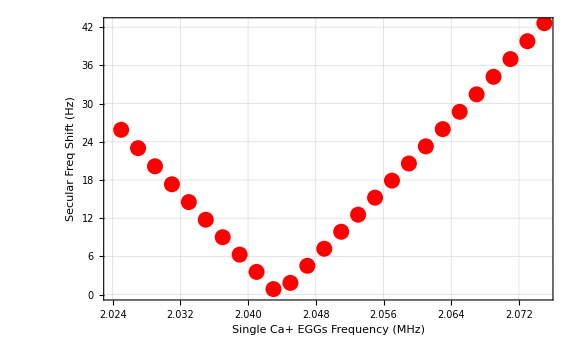

```mathematica
eggFreqSpan = Table[eggsFreq, {eggsFreq, 2.025, 2.075,.002}];
freqShift = Table[SimDiffSecFreqs[.710,eggsFreq-.3,eggsFreq], {eggsFreq, eggFreqSpan}];
shiftData = Transpose@{eggFreqSpan, freqShift};
secondNullPlot = ListPlot[shiftData, PlotStyle->{Red, PointSize[0.02]},
FrameLabel->{Style["Single Ca+ EGGs Frequency (MHz)", 16], Style["Secular Freq Shift (Hz)", 16]}, ImageSize->Large, Frame->{{True, False}, {True, False}},
GridLines->Automatic]
```

```mathematica
Export["\\\\eric.physics.ucla.edu\\groups\\motion\\Mathematica\\cat_interferometer\\images\\second_null_plot.jpg", secondNullPlot]
```

\\eric.physics.ucla.edu\groups\motion\Mathematica\cat_interferometer\images\second_null_plot.jpg

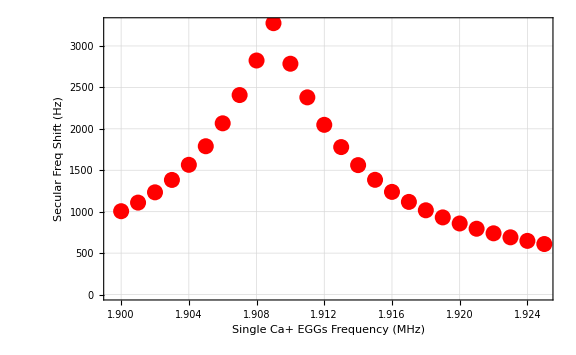

```mathematica
eggFreqSpan = Table[eggsFreq, {eggsFreq, 1.9, 1.925,.001}];
freqShift = Table[SimDiffSecFreqs[.710,eggsFreq-.3,eggsFreq], {eggsFreq, eggFreqSpan}];
shiftData = Transpose@{eggFreqSpan, freqShift};
ListPlot[shiftData, PlotStyle->{Red, PointSize[0.02]},
FrameLabel->{Style["Single Ca+ EGGs Frequency (MHz)", 16], Style["Secular Freq Shift (Hz)", 16]}, ImageSize->Large, Frame->{{True, False}, {True, False}},
GridLines->Automatic]
```

### See trend of stray fields and shift caused for different secular frequency configurations

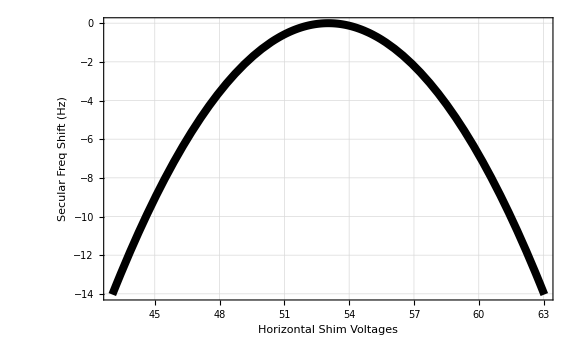

```mathematica
testSecFreqs = 2*π*{.71, 1.5, 1.8}*MHz;
secFreqs = Table[getAxialRock[getSecFreqs[{(κ*(Volt-voltMidPoint))/Sqrt[2],(κ*(Volt-voltMidPoint))/Sqrt[2],0}, massArr, testSecFreqs, knownMass, numIons, ionPositions]], {Volt, simVoltageList}];
maxSecFreq = Max[secFreqs];


Show[{Plot[(getAxialRock[getSecFreqs[{(κ*(Voltage-voltMidPoint))/Sqrt[2],(κ*(Voltage-voltMidPoint))/Sqrt[2],0}, massArr, testSecFreqs, knownMass, numIons, ionPositions]]-maxSecFreq)*MHz,
{Voltage, -voltRange/2+voltMidPoint,voltRange/2+voltMidPoint}, PlotStyle->{Black, Thickness->0.01}]},
FrameLabel->{Style["Horizontal Shim Voltages", 16], Style["Secular Freq Shift (Hz)", 16]}, ImageSize->Large, Frame->{{True, False}, {True, False}},
GridLines->Automatic
]
```

```mathematica
testSecFreqs = 2*π*{.71, 1.8, 2.1}*MHz;
secFreqs = Table[getAxialRock[getSecFreqs[{(κ*(Volt-voltMidPoint))/Sqrt[2],(κ*(Volt-voltMidPoint))/Sqrt[2],0}, massArr, testSecFreqs, knownMass, numIons, ionPositions]], {Volt, simVoltageList}];
maxSecFreq = Max[secFreqs];


Show[{Plot[(getAxialRock[getSecFreqs[{(κ*(Voltage-voltMidPoint))/Sqrt[2],(κ*(Voltage-voltMidPoint))/Sqrt[2],0}, massArr, testSecFreqs, knownMass, numIons, ionPositions]]-maxSecFreq)*MHz,
{Voltage, -voltRange/2+voltMidPoint,voltRange/2+voltMidPoint}, PlotStyle->{Black, Thickness->0.01}]},
FrameLabel->{Style["Horizontal Shim Voltages", 16], Style["Secular Freq Shift (Hz)", 16]}, ImageSize->Large, Frame->{{True, False}, {True, False}},
GridLines->Automatic
]
```

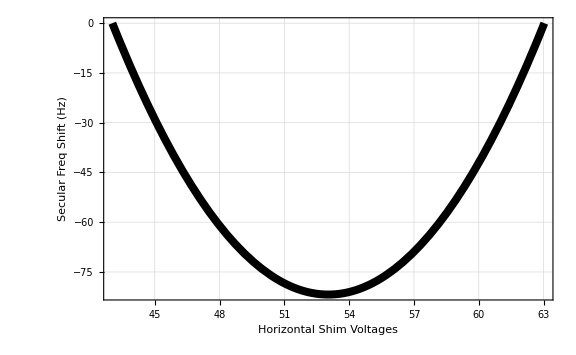

## Anharmonic Calculations

```mathematica
knownMass = 39.962590863; 
mUnknown = 36;
knownSecFreqs = 2*π*MHz*{.71, 1.3242, 1.6096}; (*Frequencies from Hao's Calibration on 06-04 - keep these and if need to change override later*)
knownSecFreqs = 2*π*MHz*{.7108, 1.299, 1.588}; 
massArr = {knownMass, mUnknown, knownMass};
EField ={0,0,0};
numIons = Length[massArr];
ionPositions = Table[{x[i], y[i], z[i]}, {i, numIons}];
ΩRF = 2*π*19.0696 * MHz;
```

```mathematica
massIndepMathieuParams= getMathieuParams[knownSecFreqs, knownMass, ΩRF];
massIndepSecFreqs = getMassIndepSecFreqs[massIndepMathieuParams, massArr, ΩRF];
U = getPotential[massArr, massIndepSecFreqs, numIons, EField, ionPositions, 0];
ionEquilibriumPositions = getEquilibriumPositions[U, numIons, ionPositions] (*this must be a different name*);
coordMasses=Flatten[ConstantArray[#,Length[First[ionPositions]]]&/@ massArr] *amu;
{evecsNormalized, secFreqsMHz} = getModeParams[U, massArr, ionEquilibriumPositions, numIons,ionPositions];
```

```mathematica
U3 = D[U, {Flatten[ionPositions], 3}]/.ionEquilibriumPositions;
U4 = D[U, {Flatten[ionPositions], 4}]/.ionEquilibriumPositions;
A3 = U3/(3! Sqrt[Outer[Times, coordMasses, coordMasses, coordMasses]]);
A4 = U4/(4! Sqrt[Outer[Times, coordMasses, coordMasses, coordMasses, coordMasses]]);
axialRockMode = evecsNormalized[[9]];


B3temp = TensorContract[TensorProduct[A3, evecsNormalized], {{1, 5}}];
C3temp = TensorContract[TensorProduct[B3temp, evecsNormalized], {{1, 5}}];
G3 = TensorContract[TensorProduct[C3temp, evecsNormalized], {{1, 5}}];

B4temp = TensorContract[TensorProduct[A4, evecsNormalized], {{1, 5}}];
C4temp = TensorContract[TensorProduct[B4temp, evecsNormalized], {{1, 5}}];
D4temp = TensorContract[TensorProduct[C4temp, evecsNormalized], {{1, 5}}];
G4 = TensorContract[TensorProduct[D4temp, evecsNormalized], {{1, 5}}];
```

```mathematica
numModes = Length[Flatten[ionPositions]];
nMax = 6; (* Size of the matrix (N x N) *)
a = Table[If[i == j - 1, Sqrt[j - 1], 0], {i, 1, nMax}, {j, 1, nMax}];
id = SparseArray[IdentityMatrix[nMax]];
aSparse = SparseArray[a, {nMax, nMax}];
ad = ConjugateTranspose[aSparse];
aMultiMode[q_]:=
  KroneckerProduct @@ Table[
    If[m == q, aSparse, id],
    {m, 1, numModes}
  ];
adMultiMode[q_] := ConjugateTranspose[aMultiMode[q]]
xMultiMode[q_]:= adMultiMode[q] + aMultiMode[q]
fockVacuum = SparseArray[UnitVector[nMax, 1], {nMax}];
multiFockState = KroneckerProduct @@ ConstantArray[fockVacuum, numModes];
multiFockSparse = SparseArray[{1->1}, {nMax^numModes}];
```

```mathematica
ll[q_]:= Sqrt[ℏ/(2*2*π*secFreqsMHz[[q]]*MHz)];
quarticDiagonalTerms[nList_]:=Sum[ll[i]^4*G4[[i,i,i,i]]*(6*nList[[i]]^2+6*nList[[i]]+3), {i,1,numModes}]
quarticOffDiagonalTerms[nList_]:=Sum[6*ll[i]^2*ll[j]^2*G4[[i,i,j,j]]*(2*nList[[i]]+1)*(2*nList[[j]]+1), {i,1,numModes-1}, {j,i+1,numModes}]
firstOrderPert[nList_]:= quarticDiagonalTerms[nList] + quarticOffDiagonalTerms[nList];
```

```mathematica
(*Construct Matrix Elements*)
x3Element[m_, n_]:= (Sqrt[(n+1)*(n+2)*(n+3)]*KroneckerDelta[m, n+3]
								+3*(n+1)^(3/2)*KroneckerDelta[m, n+1]
								+ 3*n^(3/2)*KroneckerDelta[m, n-1]
								+ Sqrt[(n)*(n-1)*(n-2)]*KroneckerDelta[m, n-3]
								);
x2Element[m_, n_]:= (Sqrt[(n+1)*(n+2)]*KroneckerDelta[m,n+2]
					+ (2*n+1)*KroneckerDelta[m, n]
					+ Sqrt[n*(n-1)]*KroneckerDelta[m, n-2]
					);								
x1Element[m_, n_]:= Sqrt[n+1]KroneckerDelta[m,n+1] + Sqrt[n]*KroneckerDelta[m,n-1];	

				
(*Construct Amplitudes*)											
cubicDiagonalTerm[mList_, nList_]:= Sum[G3[[i,i,i]]*ll[i]^3*
										x3Element[mList[[i]], nList[[i]]]*
										Product[KroneckerDelta[mList[[q]], nList[[q]]], {q, DeleteCases[Range[numModes], i]}]
										,
										{i, 1, numModes}];
cubicOffDiagonalTerm[mList_, nList_]:= (Sum[3*G3[[i,j,j]]*ll[j]^2*ll[i]
										* x1Element[mList[[i]], nList[[i]]]
										* x2Element[mList[[j]], nList[[j]]]
										* Product[
									        KroneckerDelta[mList[[q]], nList[[q]]],
									        {q, Complement[Range[numModes], {i, j}]}]
									    + 3*G3[[i,i,j]]*ll[i]^2*ll[j]*
										x1Element[mList[[j]], nList[[j]]]* x2Element[mList[[i]], nList[[i]]]
										*  Product[
									        KroneckerDelta[mList[[q]], nList[[q]]],
									        {q, Complement[Range[numModes], {i, j}]}
									     ],
										{i, 1, numModes-1},
										{j, i+1, numModes}
										]
										+ 
										Sum[
										6*G3[[i,j,k]]*ll[i]*ll[j]*ll[k]
										* x1Element[mList[[i]], nList[[i]]]
										* x1Element[mList[[j]], nList[[j]]] 
										* x1Element[mList[[k]], nList[[k]]]
										* Product[
								        KroneckerDelta[mList[[q]], nList[[q]]],
								        {q, Complement[Range[numModes], {i, j, k}]}],
										{i, 1, numModes-2},
										{j, i+1, numModes-1},
										{k, j+1, numModes}]
										);
										
cubicMatrixElement[mList_, nList_]:= cubicDiagonalTerm[mList, nList] + cubicOffDiagonalTerm[mList, nList];

secOrderPertEle[mList_, nList_]:= Abs[cubicMatrixElement[mList, nList]]^2/(Total[ℏ*2*π*MHz*secFreqsMHz*nList]-Total[ℏ*2*π*MHz*secFreqsMHz*mList]);
secOrderPert[intermediateStates_, nList_]:=Sum[
secOrderPertEle[mList, nList], 
{mList, intermediateStates}
]
```

```mathematica
(*Create all connected basis states to a nList*)

createCandidateStates[nList_]:=Module[{states},
	states = {};
	(*x3 term all excitations on one mode*);
	Do[
	states = Join[states, 
	Table[
	nList+d*UnitVector[numModes, q], 
	{d, {-3,-1,1,3}}
	]
	],
	{q, 1, numModes}
	];
	(*1 x2 term and 1 x1 term - two excitations on one mode and one excitations one another mode*)
	Do[
	states = Join[states, 
	Catenate @ Table[
	nList
	+di*UnitVector[numModes, q1]
	+dj*UnitVector[numModes, q2],
	{di, {-2,0,2}},
	{dj, {-1,1}}
	]
	],
	{q1, 1, numModes-1},
	{q2, q1+1, numModes}
	];
	Do[
	states = Join[states, 
	Catenate @ Table[
	nList
	+di*UnitVector[numModes, q2]
	+dj*UnitVector[numModes, q1],
	{di, {-2,0,2}},
	{dj, {-1,1}}
	]
	],
	{q1, 1, numModes-1},
	{q2, q1+1, numModes}
	];
	(*3 x1 terms -  all excitations on different modes*);
	Do[
	states = Join[states, 
	Catenate @ Catenate @ Table[
	nList
	+di*UnitVector[numModes, q1]
	+dj*UnitVector[numModes, q2]
	+dk*UnitVector[numModes, q3],
	{di, {-1,1}},
	{dj, {-1,1}},
	{dk, {-1,1}}
	]
	],
	{q1, 1, numModes-2},
	{q2, q1+1, numModes-1},
	{q3, q2+1, numModes}
	];
	states = Select[states, Min[#]>=0 &];
	DeleteDuplicates[states]
	]
```

```mathematica
(*Second Order Perturbation Calculation*)
intermediateStates = DeleteCases[createCandidateStates[nList], nList];
Sum[
secOrderPertEle[mList, nList], 
{mList, intermediateStates}
]
```

-3.31451×10^-33

```mathematica
calcSecFreqShifts[nList_, q_]:= Module[{intermediateStates, intermediateStatesExcited, excitedState, shift},
	excitedState = nList + UnitVector[numModes, q];
	intermediateStates = DeleteCases[createCandidateStates[nList], nList];
	intermediateStatesExcited = DeleteCases[createCandidateStates[excitedState], excitedState];
	shift = 
	(firstOrderPert[excitedState] + secOrderPert[intermediateStatesExcited, excitedState]) /(2*π*ℏ) - (firstOrderPert[nList] + secOrderPert[intermediateStates, nList]) /(2*π*ℏ)
]
```

```mathematica
nList=ConstantArray[0, numModes]
```

{0,0,0,0,0,0,0,0,0}

```mathematica
Table[calcSecFreqShifts[nList +i* UnitVector[numModes, 9], 9], {i, 0, 15}]
```

{-33.7591,-41.2525,-48.7458,-56.2392,-63.7326,-71.226,-78.7194,-86.2128,-93.7061,-101.2,-108.693,-116.186,-123.68,-131.173,-138.666,-146.16}

```mathematica
Table[calcSecFreqShifts[nList +i* UnitVector[numModes, 1], 1], {i, 0, 15}]
```

{-0.261148,0.835006,1.93116,3.02731,4.12347,5.21962,6.31578,7.41193,8.50808,9.60424,10.7004,11.7965,12.8927,13.9889,15.085,16.1812}

```mathematica
Join@@Table[{-UnitVector[numModes,q],UnitVector[numModes,q]},{q,1,numModes}]
```

{{-1,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0},{0,-1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0},{0,0,-1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0},{0,0,0,-1,0,0,0,0,0},{0,0,0,1,0,0,0,0,0},{0,0,0,0,-1,0,0,0,0},{0,0,0,0,1,0,0,0,0},{0,0,0,0,0,-1,0,0,0},{0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,-1,0,0},{0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,-1,0},{0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,-1},{0,0,0,0,0,0,0,0,1}}

```mathematica
Table[{-UnitVector[numModes,q],UnitVector[numModes,q]},{q,1,numModes}]
```

{{{-1,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0}},{{0,-1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0}},{{0,0,-1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0}},{{0,0,0,-1,0,0,0,0,0},{0,0,0,1,0,0,0,0,0}},{{0,0,0,0,-1,0,0,0,0},{0,0,0,0,1,0,0,0,0}},{{0,0,0,0,0,-1,0,0,0},{0,0,0,0,0,1,0,0,0}},{{0,0,0,0,0,0,-1,0,0},{0,0,0,0,0,0,1,0,0}},{{0,0,0,0,0,0,0,-1,0},{0,0,0,0,0,0,0,1,0}},{{0,0,0,0,0,0,0,0,-1},{0,0,0,0,0,0,0,0,1}}}

```mathematica
Join
```

```mathematica
lists={{{1,2},{3,4},{5,6}}};
Join@@lists
```

{{1,2},{3,4},{5,6}}